#### Log Plots

```mathematica
hx=0.01;
ht=0.01;

length = Floor[20/hx];
time =Floor[3/ht];
xi= Array[(#-length/2 -1)*hx&,{length+1}];
ti= Array[(#-1)*ht&,{time+1}];
```

```mathematica
StMax=ConstantArray[0,{14, 13,2}];
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9};
AlphaValues={0,.1,.25,0.5};
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.};
AlphaValues={0,.1,.25,0.5,1,2,3,4,5,6,7,8,9,10};
```

```mathematica
θ=0;
α=3;

For[j=1,j<15,j++,

β=BetaValues[[j]];

A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\Phase Portrait\\StMax_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>".csv"];

For[n=1,n<14,n++,
StMax[[j,n,2]]=Log[Norm[A[[n+7]]]];
StMax[[j,n,1]]=Log[0.1*(n+7)];

];

]
```

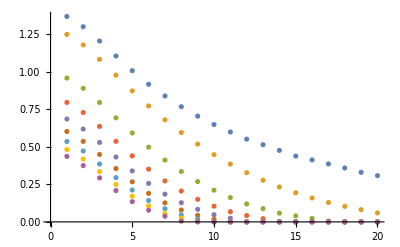

```mathematica
ListPlot[{Log[StMax[[1]]],Log[StMax[[2]]],Log[StMax[[3]]],Log[StMax[[4]]],Log[StMax[[5]]],Log[StMax[[6]]],Log[StMax[[7]]],Log[StMax[[8]]],Log[StMax[[9]]]}]
```

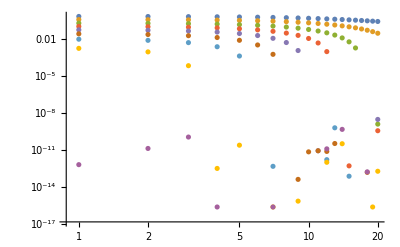

```mathematica
ListLogLogPlot[{Log[StMax[[1]]],Log[StMax[[2]]],Log[StMax[[3]]],Log[StMax[[4]]],Log[StMax[[5]]],Log[StMax[[6]]],Log[StMax[[7]]],Log[StMax[[8]]],Log[StMax[[9]]]}, PlotRange->All]
```

```mathematica
bestFitSlope[data_]:=Module[{lm,x},lm=LinearModelFit[data,{1,x},x];
First@Pick[lm["BestFitParameters"],lm["BasisFunctions"],x]];
```

```mathematica
bestFitSlope[Log[StMax[[2]]]]
```

-0.0642612

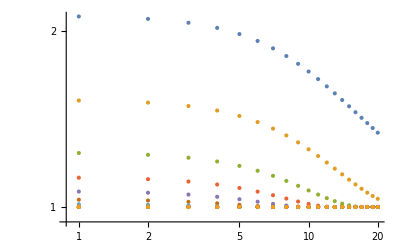

```mathematica
ListLogLogPlot[{StMax[[1]],StMax[[2]],StMax[[3]],StMax[[4]],StMax[[5]],StMax[[6]],StMax[[7]],StMax[[8]],StMax[[9]],StMax[[10]],StMax[[11]],StMax[[12]],StMax[[13]]}, PlotRange->All]
```

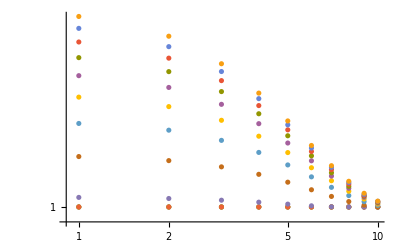

```mathematica
ListLogLogPlot[{StMax[[1]],StMax[[2]],StMax[[3]],StMax[[4]],StMax[[5]],StMax[[6]],StMax[[7]],StMax[[8]],StMax[[9]],StMax[[10]],StMax[[11]],StMax[[12]],StMax[[13]]}, PlotRange->All]
```

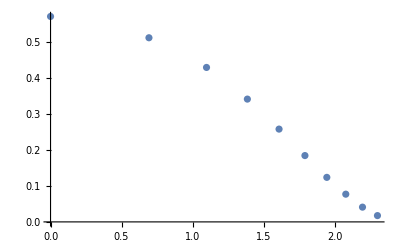

```mathematica
ListPlot[StMax[[13]]]
```

```mathematica
Slope=ConstantArray[0,14];
```

```mathematica
For[i=1,i<15,i++,
Slope[[i]]=bestFitSlope[StMax[[i]]];
]
```

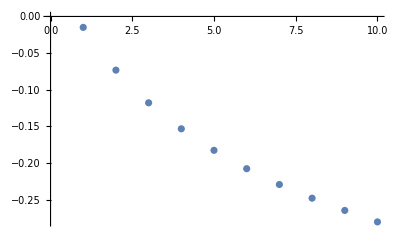

```mathematica
ListPlot[Slope]
```

```mathematica
Slope=Delete[Slope,1]
```

{-0.0148935,-0.0732072,-0.117788,-0.153231,-0.182595,-0.207652,-0.229225,-0.247875,-0.264594,-0.280226}

```mathematica
bestFitSlope[Slope]
```

-0.0280677

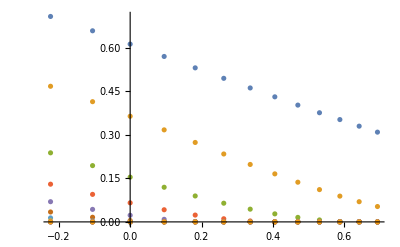

```mathematica
ListPlot[{StMax[[1]],StMax[[2]],StMax[[3]],StMax[[4]],StMax[[5]],StMax[[6]],StMax[[7]],StMax[[8]],StMax[[9]],StMax[[10]],StMax[[11]],StMax[[12]],StMax[[13]]}, PlotRange->All]
```

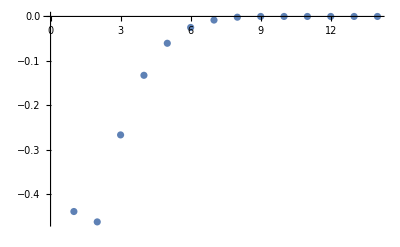

```mathematica
ListPlot[Slope]
```